```mathematica
Clear[frand,c,k,δc,randc,PAZ,tMA,PAZ100,TempsRand,TempsBestFit,PAZrand,PAZrand1003010,PAZsummary55,PAZsummary93,cK,α,β,g2]
```

```mathematica
g2[r_,β_,α_]:=(((1-r^β)/β)^α-1)/α
```

```mathematica
c={{5.631017,-4.910332,-8.51756,-9.44956},{0.186520,0.194445,0.12659,0.16267},{-10.455390,-9.610091,-20.99225,-24.58409},{0,0,0.29845,-0.86258}};
δc={{.2,0.09,1,1},{.007,0.006,0.02,0.03},{.3,0.2,6,8},{0,0,0.1,0.2}};
cK={{-21.589968,-62.8742},{0.000796839,1.3060},{-21.259381,-85.4861},{0.000558969,-8.3589}};
β={-10.058835,-9.1435};
α={-0.34055399,-0.3900};
randc[μ_,σ_]:=RandomVariate[NormalDistribution[μ,σ],1][[1]]
tMa[t_]:=3.156 10^7 10^6 t
```

```mathematica
TempsRand[r_,t_]:={randc[c[[3,1]],δc[[3,1]]]/R(Log[1-r]-(randc[c[[1,1]],δc[[1,1]]]+randc[c[[2,1]],δc[[2,1]]] Log[t]))^-1,
1/R(Exp[1/randc[c[[3,2]],δc[[3,2]]](Log[1-r]-(randc[c[[1,2]],δc[[1,2]]]+randc[c[[2,2]],δc[[2,2]]] Log[t]))])^-1,
1/R(randc[c[[2,3]],δc[[2,3]]]((Log[t]-randc[c[[3,3]],δc[[3,3]]])/(Log[1-r]-randc[c[[1,3]],δc[[1,3]]]))+randc[c[[4,3]],δc[[4,3]]])^-1,1/R(Exp[randc[c[[2,4]],δc[[2,4]]]((Log[t]-randc[c[[3,4]],δc[[3,4]]])/(Log[1-r]-randc[c[[1,4]],δc[[1,4]]]))+randc[c[[4,4]],δc[[4,4]]]])^-1};
```

```mathematica
TempsBestFit[r_,t_]:={c[[3,1]]/R(Log[1-r]-(c[[1,1]]+c[[2,1]] Log[t]))^-1,
1/R(Exp[1/c[[3,2]](Log[1-r]-(c[[1,2]]+c[[2,2]] Log[t]))])^-1,
1/R(c[[2,3]]((Log[t]-c[[3,3]])/(Log[1-r]-c[[1,3]]))+c[[4,3]])^-1,1/R(Exp[c[[2,4]]((Log[t]-c[[3,4]])/(Log[1-r]-c[[1,4]]))+c[[4,4]]])^-1}
TempsKetcham[r_,t_]:={(cK[[2,1]]((Log[t]-cK[[3,1]])/(g2[r,β[[1]],α[[1]]]-cK[[1,1]]))+cK[[4,1]])^-1,(Exp[cK[[2,2]]((Log[t]-cK[[3,2]])/(g2[r,β[[2]],α[[2]]]-cK[[1,2]]))+cK[[4,2]]])^-1}
```

```mathematica
PAZ[r_,t_]:=Table[TempsBestFit[r,t][[i]]-273.15,{i,1,4,1}]
PAZK[r_,t_]:=Table[TempsKetcham[r,t][[i]]-273.15,{i,1,2,1}]
PAZ1003010=Table[{PAZ[0.55,tMa[t]],PAZ[0.93,tMa[t]]},{t,{100,30,10}}]
KetPAZ1003010=Table[{PAZK[0.55,tMa[t]],PAZK[0.93,tMa[t]]},{t,{100,30,10}}]
```

{{{128.908,101.803,136.641,110.71},{78.8551,35.7986,57.2122,8.23178}},{{135.928,111.049,143.338,119.5},{84.2244,43.4172,62.9527,16.4658}},{{142.551,119.685,149.643,127.695},{89.2688,50.5329,68.3677,24.1892}}}

{{{131.035,96.8683},{55.0348,21.6873}},{{137.759,105.969},{60.7999,29.6211}},{{144.094,114.468},{66.2402,37.0467}}}

```mathematica
PAZ1003010[[3,2,4]]
```

24.1892

```mathematica
R=1.987204258 10^-3;
```

```mathematica
k=300000;
```

```mathematica
PAZrand[r_,t_]=Table[Table[TempsRand[r,t][[i]]-273.15,{i,1,4,1}],{j,1,k}];
```

```mathematica
PAZrand1003010=Table[{PAZrand[0.55,tMa[t]],PAZrand[0.93,tMa[t]]},{t,{100,30,10}}]
```

{{{{154.843,89.1464,201.977,39.0546},{125.397,113.925,155.045,98.382},{123.696,104.116,203.111,-110.129},299994,{120.257,104.662,181.512,94.1958},{140.296,97.5586,130.074,321.747},{90.4508,97.3685,121.578,90.7054}},{1}},{1},{1}}
 |  |  |  |

```mathematica
PAZrand1003010[[3,1,10,4]]
```

72.8405

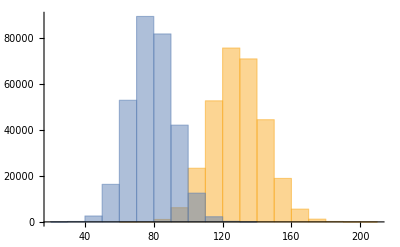
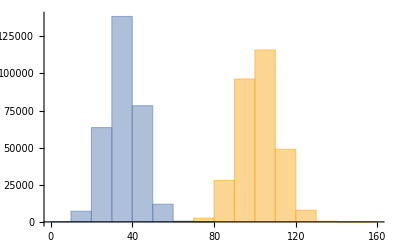
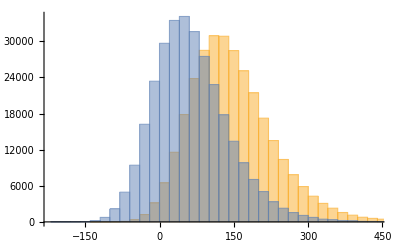
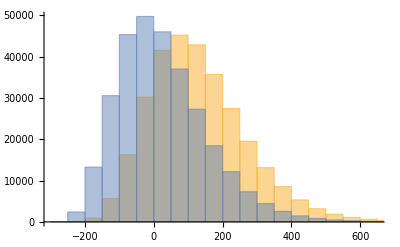
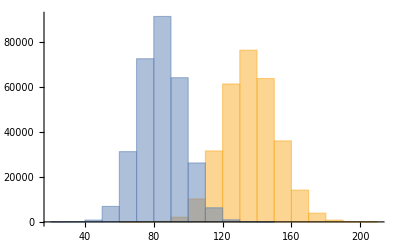
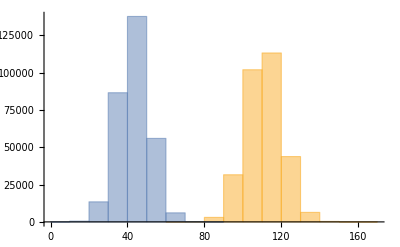
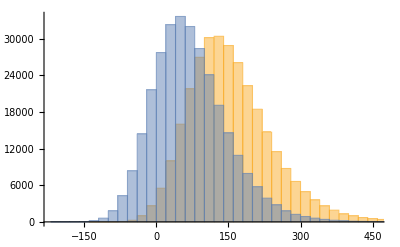
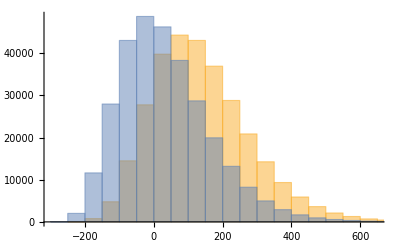

```mathematica
Table[Table[Histogram[{Table[PAZrand1003010[[t,1,i,j]],{i,1,k}],Table[PAZrand1003010[[t,2,i,j]],{i,1,k}]}],{j,1,4}],{t,1,3}]
```

```mathematica
halfdist=Table[Table[Table[Select[PAZrand1003010[[t,j,;;,i]],#<PAZ1003010[[t,j,i]]&],{i,1,4}],{j,1,2}],{t,1,3}];
```

```mathematica
σ55=Table[Table[√(Sum[(halfdist[[l,1,t,i]]-PAZ1003010[[l,1,t]])^2,{i,1,Length[halfdist[[l,1,t]]]}]/(Length[halfdist[[l,1,t]]]-1)),{t,1,4}],{l,1,3}];
```

```mathematica
σ93=Table[Table[√(Sum[(halfdist[[l,2,t,i]]-PAZ1003010[[l,2,t]])^2,{i,2,Length[halfdist[[l,2,t]]]}]/(Length[halfdist[[l,2,t]]]-1)),{t,1,4}],{l,1,3}];
```

```mathematica
PAZ100summary=Join[{{"r = 0.55","σ55","r = 0.93","σ93"}},{{PAZ1003010[[1,1,;;]],σ55[[1,;;]],PAZ1003010[[1,2,;;]],σ93[[1,;;]]}}]//TableForm
```

r = 0.55 | σ55 | r = 0.93 | σ93
128.908
101.803
136.641
110.71 | 14.7909
9.25527
67.1258
111.008 | 78.8551
35.7986
57.2122
8.23178 | 12.3569
8.04722
62.4915
98.84956

```mathematica
PAZ30summary=Join[{{"r = 0.55","σ55","r = 0.93","σ93"}},{{PAZ1003010[[2,1,;;]],σ55[[2,;;]],PAZ1003010[[2,2,;;]],σ93[[2,;;]]}}]//TableForm
```

r = 0.55 | σ55 | r = 0.93 | σ93
135.928
111.049
143.338
119.5 | 15.0289
9.184
68.3324
112.664 | 84.2244
43.4172
62.9527
16.4658 | 12.5237
7.98697
63.5932
100.872

```mathematica
PAZ10summary=Join[{{"r = 0.55","σ55","r = 0.93","σ93"}},{{PAZ1003010[[3,1,;;]],σ55[[3,;;]],PAZ1003010[[3,2,;;]],σ93[[3,;;]]}}]//TableForm
```

r = 0.55 | σ55 | r = 0.93 | σ93
142.551
119.685
149.643
127.695 | 15.2552
9.11339
69.4565
114.218 | 89.2688
50.5329
68.3677
24.1892 | 12.6789
7.92723
64.6456
102.72

```mathematica
KetPAZ100summary=Join[{{"r = 0.55","r = 0.93"}},{{KetPAZ1003010[[1,1,;;]],KetPAZ1003010[[1,2,;;]]}}]//TableForm
```

r = 0.55 | r = 0.93
131.035
96.8683 | 55.0348
21.6873

```mathematica
KetPAZ30summary=Join[{{"r = 0.55","r = 0.93"}},{{KetPAZ1003010[[2,1,;;]],KetPAZ1003010[[2,2,;;]]}}]//TableForm
```

r = 0.55 | r = 0.93
137.759
105.969 | 60.7999
29.6211

```mathematica
KetPAZ10summary=Join[{{"r = 0.55","r = 0.93"}},{{KetPAZ1003010[[3,1,;;]],KetPAZ1003010[[3,2,;;]]}}]//TableForm
```

r = 0.55 | r = 0.93
144.094
114.468 | 66.2402
37.0467